# Simulating BZ Life Forms using a Phenomenological Model

#### Abhishek Sharma Cronin Lab University of Glasgow

THIS FILE RUNS THE SIMULATIONS OF BZ LIFE FORMS (CHEMITS). IT SHOULD BE NOTED THAT THERE IS A POSSIBILITY THAT THE OUTPUT GENERATED FROM THE SIMULATIONS MIGHT BE DIFFERENT DUE TO RANDOM SEED. HOWEVER, IT HAS BEEN TESTED THAT THE STATISTICALLY IT GIVES THE SAME DISTRIBUTION OVER POPULATION AND OTHER PROPERTIES.

```mathematica
SeedRandom[111]
```

RandomGeneratorState[…]

```mathematica
baseDirectory=NotebookDirectory[]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/

## BZ Life Form: Finite State Machine for Cell Stirrers

```mathematica
initCAState[nCells_,initLF_]:=Module[{CAState,initPos},CAState=ConstantArray[0,{nCells, nCells}];initPos=RandomInteger[{1,nCells},{2}]&/@Range[initLF];
Table[CAState⟦initPos⟦i,1⟧,initPos⟦i,2⟧⟧=1,{i,Length[initPos]}];
Return[CAState]]
```

```mathematica
initPWMState[CAState_,randomS_,nCells_]:=Module[{boundC,PWMState,randomPos,nPos,lfPos},
boundC[{x_,y_}]:={ Which[x==0,nCells,x==nCells+1,1,x>0&&x<nCells+1,x],Which[y== 0,nCells,y==nCells+1,1,y>0&&y<nCells+1,y]};
PWMState=ConstantArray[1,{nCells, nCells}];
randomPos=RandomInteger[{1,nCells},{2}]&/@Range[randomS];
Table[PWMState⟦randomPos⟦i,1⟧,randomPos⟦i,2⟧⟧=2,{i,Length[randomPos]}];
lfPos=Position[CAState,1];
nPos=Flatten[{{#⟦1⟧-1,#⟦2⟧},{#⟦1⟧+1,#⟦2⟧},{#⟦1⟧,#⟦2⟧-1},{#⟦1⟧,#⟦2⟧+1}}&/@lfPos,1];
nPos=boundC[#]&/@nPos;
Table[PWMState⟦nPos⟦i,1⟧,nPos⟦i,2⟧⟧=4,{i,Length[nPos]}];
Table[PWMState⟦lfPos⟦i,1⟧,lfPos⟦i,2⟧⟧=3,{i,Length[lfPos]}];
Return[PWMState]]
```

```mathematica
bzlifeFSM[CAState_,PWMState_,randomS_,nCells_]:=Module[{boundC,nPWMState,chMat,lfPos,nnList,nnnList,rand,nList,nnCAList,nnPWMList,nnnCAList,nnCells,nnnCells,sCell,cnt=0},
boundC[x_,y_]:={ Which[x==0,nCells,x==nCells+1,1,x>0&&x<nCells+1,x],Which[y== 0,nCells,y==nCells+1,1,y>0&&y<nCells+1,y]};
nPWMState=ConstantArray[1,Dimensions[PWMState]];
chMat= ConstantArray[0,Dimensions[PWMState]]; (* Array to track if changes are possible *)
lfPos=Position[PWMState,3];
(nPWMState⟦#⟦1⟧,#⟦2⟧⟧=3)&/@lfPos;
nnList={{#⟦1⟧-1,#⟦2⟧},{#⟦1⟧+1,#⟦2⟧},{#⟦1⟧,#⟦2⟧-1},{#⟦1⟧,#⟦2⟧+1}}&/@lfPos;
nnnList={{#⟦1⟧+1,#⟦2⟧+1},{#⟦1⟧+1,#⟦2⟧-1},{#⟦1⟧-1,#⟦2⟧+1},{#⟦1⟧-1,#⟦2⟧-1}}&/@lfPos;
nnList=Apply[boundC,nnList,{2}];
nnnList=Apply[boundC,nnnList,{2}];
nnCAList=Table[CAState⟦#⟦1⟧,#⟦2⟧⟧&/@nnList⟦i⟧,{i,Length[lfPos]}];
nnPWMList=Table[PWMState⟦#⟦1⟧,#⟦2⟧⟧&/@nnList⟦i⟧,{i,Length[lfPos]}];
nnnCAList=Table[CAState⟦#⟦1⟧,#⟦2⟧⟧&/@nnnList⟦i⟧,{i,Length[lfPos]}];
nnCells=Block[{caPos},caPos=Flatten[Position[nnCAList⟦#⟧,1]]
&/@Range[Length[lfPos]];
Which[Length[caPos⟦#⟧]== 0,{},Length[caPos⟦#⟧]==1,caPos⟦#⟧,Length[caPos⟦#⟧]>1,rand=RandomInteger[{1,Length[caPos⟦#⟧]}];{caPos⟦#,rand⟧}]&/@Range[Length[lfPos]]];

nnnCells=Block[{caPos},caPos=Flatten[Position[nnnCAList⟦#⟧,1]]
&/@Range[Length[lfPos]]; 
Which[Length[caPos⟦#⟧]== 0,{},Length[caPos⟦#⟧]==1,caPos⟦#⟧,Length[caPos⟦#⟧]>1,rand=RandomInteger[{1,Length[caPos⟦#⟧]}];{caPos⟦#,rand⟧}]&/@Range[Length[lfPos]]];

sCell=Which[
Length[nnCells⟦#⟧]==0&&Length[nnnCells⟦#⟧]==1,{2,#,nnnCells⟦#⟧,lfPos⟦#⟧,First@nnnList⟦#,nnnCells⟦#⟧⟧},
Length[nnCells⟦#⟧]==1&&Length[nnnCells⟦#⟧]==0,{1,#,nnCells⟦#⟧,lfPos⟦#⟧,First@nnList⟦#,nnCells⟦#⟧⟧},
Length[nnCells⟦#⟧]==1&&Length[nnnCells⟦#⟧]==1,If[RandomInteger[]==1,{1,#,nnCells⟦#⟧,lfPos⟦#⟧,First@nnList⟦#,nnCells⟦#⟧⟧},{2,#,nnnCells⟦#⟧,lfPos⟦#⟧,First@nnnList⟦#,nnnCells⟦#⟧⟧}]]&/@Range[Length[lfPos]]/.Null->Sequence[];

(* Propagation and Replication Events *)
If[#⟦1⟧==1,
If[PWMState⟦#⟦5,1⟧,#⟦5,2⟧⟧==3,
If[RandomInteger[]==0,
nPWMState⟦#⟦4,1⟧,#⟦4,2⟧⟧=3,nPWMState⟦#⟦4,1⟧,#⟦4,2⟧⟧=1],
nPWMState⟦#⟦4,1⟧,#⟦4,2⟧⟧=1;nPWMState⟦#⟦5,1⟧,#⟦5,2⟧⟧=3;
chMat⟦#⟦4,1⟧,#⟦4,2⟧⟧=1]]&/@sCell; 
If[#⟦1⟧==2,nPWMState⟦#⟦5,1⟧,#⟦5,2⟧⟧=3]&/@sCell;
(chMat⟦#⟦1⟧,#⟦2⟧⟧=1)&/@Evaluate[Position[nPWMState,3]];

lfPos=Position[nPWMState,3];
nnList={{#⟦1⟧-1,#⟦2⟧},{#⟦1⟧+1,#⟦2⟧},{#⟦1⟧,#⟦2⟧-1},{#⟦1⟧,#⟦2⟧+1}}&/@lfPos;
nnList=Flatten[Apply[boundC,nnList,{2}],1];
If[chMat⟦#⟦1⟧,#⟦2⟧⟧≠1,nPWMState⟦#⟦1⟧,#⟦2⟧⟧=4]&/@nnList;
(chMat⟦#⟦1⟧,#⟦2⟧⟧=1)&/@nnList;

Block[{pos},While[cnt≠randomS,pos=RandomInteger[{1,nCells},{2}];If[chMat⟦pos⟦1⟧,pos⟦2⟧⟧≠1,nPWMState⟦pos⟦1⟧,pos⟦2⟧⟧=2;chMat⟦pos⟦1⟧,pos⟦2⟧⟧=1;cnt=cnt+1];]];
Return[nPWMState]]
```

## BZ Life Form: Phenomenological Model for updating CA states

In this section, we develop the phenomenological model for updating the CA states based on the current CA state of cell and its neighbours and applied PWM Levels. 

CA_state^(t+1)= f(CA_state^t, PWM_state^t)

Due to complex hydrodynamic coupling between the cells, we define probabilities of updating states based on the given set of PWM levels and CA states. Here we write down the list of probabilities for different possible combinations : 
Cell State 0 : Light Blue (Weak Oscillations)
Cell State 1 : Dark Blue (Strong Oscillations)

→ if (nPWM_3 ≥ 3): 𝒫(0) =, 𝒫(1) =
→ else if (nPWM_3 is ≥ 1 and nPWM_3 < 3): 𝒫(0) =, 𝒫(1) =
→ else if (nPWM_4 ≥ 3): 𝒫(0) =, 𝒫(1) =
→ else if (nPWM_4 is ≥ 1 and nPWM_4 < 3): 𝒫(0) =, 𝒫(1) =

To update CA states, we will iterate through all the cells and update the states based on PWM level of cell and nearest neighbours.

```mathematica
facCellType=0.7;
```

```mathematica
prob1=0.50;(* When nCells with PWM(3)≥3 *)
```

```mathematica
prob2=0.30;(* When nCells with PWM(3)<3 *)
```

```mathematica
prob3=0.25;(* When nCells with PWM(3)==0 and When nCells with PWM(4)≥3 *)
```

```mathematica
prob4=0.15;(* When nCells with PWM(3)==0 and When nCells with PWM(4)<3 *)
```

```mathematica
fac1=0.0; (* When Cell PWM is 1 *)
```

```mathematica
fac2=0.1 ;(* When Cell PWM is 2 *)
```

```mathematica
fac3=0.5;(* When Cell PWM is 4 *)
```

```mathematica
probHigh=0.5;(* When Cell PWM is 3 *)
```

```mathematica
updateCellState[{i_,j_},{CAState_,PWMState_},nCells_]:=Block[{boundC,cellCA=CAState⟦i,j⟧,cellPWM=PWMState⟦i,j⟧,nList,nPWM,nPWM3,nPWM4,prob},
nList={{i-1,j},{i+1,j},{i,j-1},{i,j+1}};
boundC[x_,y_]:={ Which[x==0,nCells,x==nCells+1,1,x>0&&x<nCells+1,x],Which[y== 0,nCells,y==nCells+1,1,y>0&&y<nCells+1,y]};
nList=Flatten[Apply[boundC,{nList},{2}],1];(* Getting neighbour lists *)
nPWM=PWMState⟦#⟦1⟧,#⟦2⟧⟧&/@nList;(* Getting neighbour PWM levels *)
nPWM3=Length@Position[nPWM,3];(* Getting number of neighbours with PWM levels 3 *)
nPWM4=Length@Position[nPWM,4];(* Getting number of neighbours with PWM levels 4 *)
prob=Which[nPWM3≥3,prob1,nPWM3<3 && nPWM3≥1,prob2,nPWM3==0 && nPWM4≥3 ,prob3,nPWM3==0 && nPWM4<3&& nPWM4≥1,prob4,nPWM3==0 && nPWM4==0,0];
Return[Block[{prob1},Which[cellCA== 0,
prob1=facCellType Which[cellPWM==1,prob fac1,cellPWM==2,prob fac2,cellPWM==3,probHigh,cellPWM==4,prob fac3];
RandomChoice[{prob1,1-prob1}->{1,0}],
cellCA==1,
prob1=Which[cellPWM==1,prob fac1,cellPWM==2,prob fac2,cellPWM==3,probHigh,cellPWM==4,prob fac3];
RandomChoice[{prob1,1-prob1}->{1,0}]
]]]]
```

## Varying Simulation Size

In this section, we create different initial populations of life forms and evolve them over time. For each population number, we ran 20 experiments, to estimate the average properties.

```mathematica
runSimulation[nCells_,numRandom_,nLifeForms_,nSteps_,runID_]:=Module[{cnt=0,CAState,PWMState,allPWMStates={},allCAStates={}},
CAState=initCAState[nCells,nLifeForms]; (* Initializing CA States *)
PWMState=initPWMState[CAState,numRandom,nCells]; (* Initializing PWM States *)
Monitor[While[cnt≤ nSteps,
PWMState=bzlifeFSM[CAState,PWMState,numRandom,nCells];
CAState=Table[updateCellState[{i,j},{CAState,PWMState},nCells],{i,nCells},{j,nCells}];
allPWMStates=Join[allPWMStates,{PWMState}];
allCAStates=Join[allCAStates,{CAState}];
cnt=cnt+1],cnt];
Export[baseDirectory<>"PWM_data"<>ToString[runID]<>"_"<>ToString[nCells]<>".mx",allPWMStates];
Export[baseDirectory<>"CA_data"<>ToString[runID]<>"_"<>ToString[nCells]<>".mx",allCAStates];]
```

```mathematica
LaunchKernels[]
```

{Local,Local,Local,Local,Local,Local,Local,Local,Local,Local}

```mathematica
Clear[nCells]
nSteps=10000;nRuns=25;
nCellsAll={10,20,50,100,150};
```

```mathematica
Table[ParallelTable[runSimulation[nCellsAll⟦j⟧,nCellsAll⟦j⟧^2/10,10,nSteps,i],{i,nRuns}],{j,Length[nCellsAll]}];
```

```mathematica
analyzeAllData[nCells_,runID_]:=Module[{allPWMStates,allCAStates},
allPWMStates=Import[baseDirectory<>"PWM_data"<>ToString[runID]<>"_"<>ToString[nCells]<>".mx"];allCAStates=Import[baseDirectory<>"CA_data"<>ToString[runID]<>"_"<>ToString[nCells]<>".mx"];
Length[Position[allPWMStates⟦#⟧,3]]&/@Range[nSteps]]
```

```mathematica
popLifeForms10=analyzeAllData[10,#]&/@Range[nRuns];
```

```mathematica
popLifeForms20=analyzeAllData[20,#]&/@Range[nRuns];
```

```mathematica
popLifeForms50=analyzeAllData[50,#]&/@Range[nRuns];
```

```mathematica
popLifeForms100=analyzeAllData[100,#]&/@Range[nRuns];
```

```mathematica
popLifeForms150=analyzeAllData[150,#]&/@Range[nRuns];
```

```mathematica
Dimensions/@{popLifeForms10,popLifeForms20,popLifeForms50,popLifeForms100,popLifeForms150}
```

{{25,10000},{25,10000},{25,10000},{25,10000},{25,10000}}

```mathematica
GraphicsGrid[Partition[ListPlot[popLifeForms150⟦#⟧,PlotStyle->{Black,PointSize[0.01]},ImageSize->100,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},Frame-> True,AspectRatio->1,FrameLabel->{"Time Step","BZ Life Forms"}]&/@Range[Length[popLifeForms150]],5],Spacings->0,ImageSize->1000]
```

```mathematica
p1=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[popLifeForms10],StandardDeviation[popLifeForms10]}],AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,Opacity[ 0.02]},FrameLabel->{"Time Step","BZ Life Forms"},PlotMarkers->None,Frame-> True,PlotRange-> {0,15},Epilog->{Inset[Style["Cell Size 10 x 10",12],Scaled[{0.5,0.9}]]}],ListPlot[Mean[popLifeForms10],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 200];
```

```mathematica
p2=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[popLifeForms20],StandardDeviation[popLifeForms20]}],AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,Opacity[ 0.02]},FrameLabel->{"Time Step","BZ Life Forms"},PlotMarkers->None,Frame-> True,PlotRange-> {0,22},Epilog->{Inset[Style["Cell Size 20 x 20",12],Scaled[{0.5,0.9}]]}],ListPlot[Mean[popLifeForms20],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 200];
```

```mathematica
p3=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[popLifeForms50],StandardDeviation[popLifeForms50]}],AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,Opacity[ 0.02]},FrameLabel->{"Time Step","BZ Life Forms"},PlotMarkers->None,Frame-> True,PlotRange-> {0,60},Epilog->{Inset[Style["Cell Size 50 x 50",12],Scaled[{0.5,0.9}]]}],ListPlot[Mean[popLifeForms50],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 200];
```

```mathematica
p4=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[popLifeForms100],StandardDeviation[popLifeForms100]}],AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,Opacity[ 0.02]},FrameLabel->{"Time Step","BZ Life Forms"},PlotMarkers->None,Frame-> True,PlotRange-> {0,180},Epilog->{Inset[Style["Cell Size 100 x 100",12],Scaled[{0.5,0.9}]]}],ListPlot[Mean[popLifeForms100],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 200];
```

```mathematica
p5=Show[{ListPlot[MapThread[Around[#1,#2]&,{Mean[popLifeForms150],StandardDeviation[popLifeForms150]}],AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,Opacity[ 0.02]},FrameLabel->{"Time Step","BZ Life Forms"},PlotMarkers->None,Frame-> True,PlotRange-> {0,350},Epilog->{Inset[Style["Cell Size 150 x 150",12],Scaled[{0.5,0.9}]]}],ListPlot[Mean[popLifeForms150],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},PlotStyle->{Black,PointSize[0.01]},PlotMarkers->None,Frame-> True]},ImageSize-> 200];
```

```mathematica
plot1=GraphicsRow[{p1,p2,p3,p4,p5},Spacings->{-10,-10},ImageSize->1000]
```

```mathematica
Export[baseDirectory<>"plot1.png",plot1,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot1.png

```mathematica
Export[baseDirectory<>"plot1.svg",plot1]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot1.svg

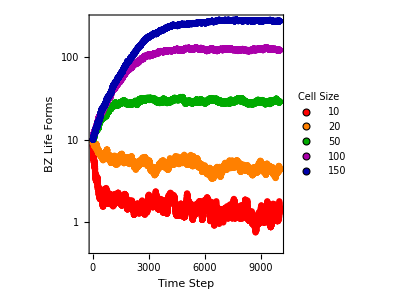

```mathematica
ListLogPlot[{Mean[popLifeForms10],Mean[popLifeForms20],Mean[popLifeForms50],Mean[popLifeForms100],Mean[popLifeForms150]},PlotStyle-> {{Red,PointSize[0.015]},{Orange,PointSize[0.015]},{Darker[Green],PointSize[0.015]},{Darker[Magenta],PointSize[0.015]},{Darker[Blue],PointSize[0.015]}},PlotRange-> Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,AspectRatio->1,FrameLabel->{"Time Step","BZ Life Forms"},PlotLegends-> Placed[LineLegend[{"10","20","50","100","150"},LegendMarkers->Graphics[Disk[]],LegendLabel-> "Cell Size",LegendLayout-> "Column",Spacings-> {0.1,0.1}],{0.16,0.8}],ImageSize->300]
```

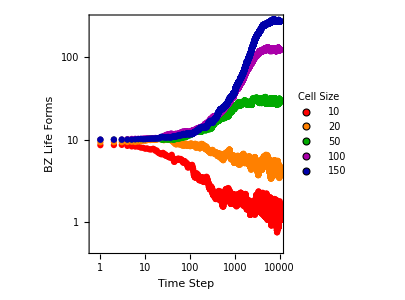

```mathematica
plot2=ListLogLogPlot[{Mean[popLifeForms10],Mean[popLifeForms20],Mean[popLifeForms50],Mean[popLifeForms100],Mean[popLifeForms150]},PlotStyle-> {{Red,PointSize[0.015]},{Orange,PointSize[0.015]},{Darker[Green],PointSize[0.015]},{Darker[Magenta],PointSize[0.015]},{Darker[Blue],PointSize[0.015]}},PlotRange-> Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,AspectRatio->1,FrameLabel->{"Time Step","BZ Life Forms"},PlotLegends-> Placed[LineLegend[{"10","20","50","100","150"},LegendMarkers->Graphics[Disk[]],LegendLabel-> "Cell Size",LegendLayout-> "Column",Spacings-> {0.1,0.1}],{0.16,0.75}],ImageSize->300]
```

```mathematica
Export[baseDirectory<>"plot2.png",plot2,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot2.png

```mathematica
Export[baseDirectory<>"plot2.svg",plot2]
```

/Users/abhisheksharma/Documents/Projects/BZ_Comptutation/BZ_SimCellSize/plot2.svg